```mathematica
data = Import ["/home/marius/MA/CUDA_Simulation_RW/Results/Histogram_05_11/histogram_gamma_0.9_nu_0.9_ta_0.txt","Table"];
```

```mathematica
nu=0.9;
x= data[[1,All]];
frames = {};

For[u = 1, u ≤Length[data],u++,
y=data[[u,All]];
hist = Transpose[{x,y}];
time = 10000/Length[data]*u;
boundry = {{time,0},{time,Max[y]}};
frame = ListLinePlot[{hist},AxesLabel->{"Distance","Relative Number of Particles"}];
AppendTo[frames,frame];
(*ListLinePlot[boundry]*)
]

Animate[ y=data[[u,All]];
hist = Transpose[{x,y}];
time = 10000/Length[data]*u;
boundry = {{time,0},{time,Max[y]}};
ListLinePlot[{hist},AxesLabel->{"Distance","Relative Number of Particles"}]
,{u,2,Length[data],1}]
```

```mathematica
Export["MA/CUDA_Simulation_RW/Results/Histogram_05_11/movie_gamma_0.9_nu_0.9_ta_0.avi",frames]
```

MA/CUDA_Simulation_RW/Results/Histogram_05_11/movie_gamma_0.9_nu_0.9_ta_0.avi

```mathematica
Length[frames]
Streams[]
```

11

{OutputStream[…],OutputStream[…],OutputStream[…]}

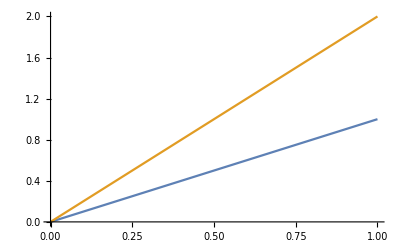

```mathematica
ListLinePlot[{{{0,0},{1,1}},{{0,0},{1,2}}}]
```